## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
?dispersion`*
```

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Needs["PolygonPlotMarkers`"]
```

```mathematica
shapes=PolygonMarker[All];
shapesTip=Table[
Tooltip[Graphics[{FaceForm[pltcolors[[i]]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[shapes[[i]],Scaled[.3]]},ImageSize->15],shapes[[i]]],
{i,1,Length@pltcolors}]
shapesTipTable={shapesTip,
Table[i,{i,1,Length@pltcolors}]}//Transpose
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,13},{-Graphics-,14},{-Graphics-,15}}

```mathematica
pltmarkers={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Discrete Beams for Comparison

```mathematica
{{
Show[NBeamsKNPlt[NBeamsLR[2],{-4.5,4.5},{-15,15}],PlotLabel->"k(n): 2 Beams with Crossing"],
Show[NBeamsKNPlt[NBeamsH[2],{-4.5,4.5},{-15,15}],PlotLabel->"k(n): 2 Beams without Crossing"]
}}//Grid
```

```mathematica
{{Show[
NBeamsKNPlt[NBeamsLR[2]],
Plot[{-0.4,-2.5},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Opacity[0.1]],Filling->{1->{2}},FillingStyle->LightRed],
ImageSize->{Automatic,500},
ImagePadding->{{Automatic, Automatic}, {Automatic,10}}],
Show[
NBeamsOmegaKPlt[NBeamsLR[2]][[2]],
Plot[{100Sign[x+0.4],100Sign[x+2.5]},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Opacity[0.1]],Filling->{1->{2}},FillingStyle->LightRed],
ImageSize->{Automatic,500},
ImagePadding->{{Automatic, Automatic}, {Automatic,10}}
]
}}//Grid
```

```mathematica
{{Show[
NBeamsOmegaNPlt[NBeamsLR[2]],
Plot[{-0.65,-1.65},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Opacity[0.1]],Filling->{1->{2}},FillingStyle->LightRed],
ImageSize->{Automatic,500},
ImagePadding->{{Automatic, Automatic}, {Automatic,10}}],
Show[
NBeamsOmegaKPlt[NBeamsLR[2]][[2]],
Plot[{-0.65,-1.65},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Opacity[0.1]],Filling->{1->{2}},FillingStyle->LightRed],
ImageSize->{Automatic,500},
ImagePadding->{{Automatic, Automatic}, {Automatic,10}}
]
}}//Grid
```

```mathematica
{{NBeamsOmegaNPlt[NBeamsLR[2]],
NBeamsOmegaNPlt[NBeamsLR[4]]},
{NBeamsOmegaNPlt[NBeamsLR[6]],
NBeamsOmegaNPlt[NBeamsLR[8]]}}//Grid
```

```mathematica
{{NBeamsOmegaKPlt[NBeamsLR[2]][[2]],
NBeamsOmegaKPlt[NBeamsLR[4]][[2]]},
{NBeamsOmegaKPlt[NBeamsLR[6]][[2]],
NBeamsOmegaKPlt[NBeamsLR[8]][[2]]}}//Grid
```

```mathematica
{{NBeamsOmegaNPlt[NBeamsH[2]],
NBeamsOmegaNPlt[NBeamsH[4]]},
{NBeamsOmegaNPlt[NBeamsH[6]],
NBeamsOmegaNPlt[NBeamsH[8]]}}//Grid
```

```mathematica
{{NBeamsOmegaKPlt[NBeamsH[2]][[2]],
NBeamsOmegaKPlt[NBeamsH[4]][[2]]},
{NBeamsOmegaKPlt[NBeamsH[6]][[2]],
NBeamsOmegaKPlt[NBeamsH[8]][[2]]}}//Grid
```

## Continuous

```mathematica
i0Homza1=IntFun0n[n,0.9,0.3]
i2Homza1=IntFun2n[n,0.9,0.3]//FullSimplify
i1Homza1=IntFun1n[n,0.9,0.3]//FullSimplify


i0Homza1abs=IntFun0n[n,c1,c2]
i2Homza1abs=IntFun2n[n,c1,c2]//FullSimplify
i1Homza1abs=IntFun1n[n,c1,c2]//FullSimplify
```

(-Log[Abs[1-0.9 n]]+Log[Abs[1-0.3 n]])/n

((-0.6-0.36 n) n+1. Log[Abs[0.333333+0.740741/(1.11111-1. n)]])/n^3

(-0.6 n+1. Log[Abs[0.333333-0.740741/(-1.11111+1. n)]])/n^2

(-Log[Abs[1-c1 n]]+Log[Abs[1-c2 n]])/n

(-(c1-c2) n (2+(c1+c2) n)+2 Log[Abs[(-1+c2 n)/(-1+c1 n)]])/(2 n^3)

((-c1+c2) n+Log[Abs[(-1+c2 n)/(-1+c1 n)]])/n^2

We can find the limits

```mathematica
Limit[
{omegaFunHoMAA1[n] n,omegaFunHoMAA1[n]},
n->1/0.3]
```

{Limit[n omegaFunHoMAA1[n],n→3.33333],Limit[omegaFunHoMAA1[n],n→3.33333]}

```mathematica
Limit[
{omegaFunHoMAA1[n] n,omegaFunHoMAA1[n]},
n->Infinity]
Limit[
{omegaFunHoMZA1[n] n,omegaFunHoMZA1[n]},
n->Infinity]
```

{Limit[n omegaFunHoMAA1[n],n→∞],Limit[omegaFunHoMAA1[n],n→∞]}

{Limit[n omegaFunHoMZA1[n],n→∞],Limit[omegaFunHoMZA1[n],n→∞]}

These limits can be calcualted without going into examples

```mathematica
Limit[{n ,1}((intFun0n[n,c1,c2]-intFun2n[n,c1,c2])/4),n->Infinity]//FullSimplify
```

{Limit[1/4 n (intFun0n[n,c1,c2]-intFun2n[n,c1,c2]),n→∞],Limit[1/4 (intFun0n[n,c1,c2]-intFun2n[n,c1,c2]),n→∞]}

```mathematica
Limit[{n ,1}( (-4(i0Homza1abs)(i2Homza1abs)+4 i1Homza1abs^2+8(i0Homza1abs+i2Homza1abs))/(-16) ),n->Infinity]//FullSimplify
```

{1/4 (c1^2-c2^2+2 Log[Abs[c1]]-2 Log[Abs[c2]]),0}

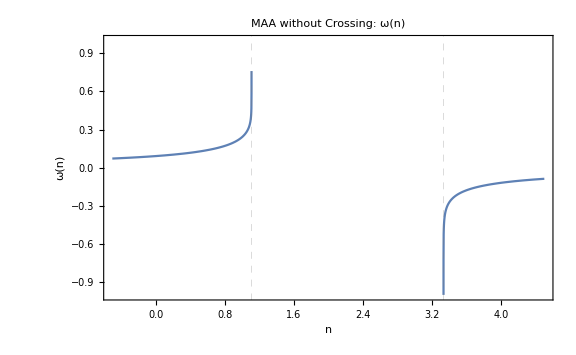

```mathematica
Plot[ConAxialSymOmegaNMAA[n,{{{0.9,0.3},1}}],{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{Automatic,{-1,1}},PlotLabel->"MAA without Crossing: ω(n)",FrameLabel->{"n","ω(n)"},Exclusions->{1/0.9,1/0.3}]
```

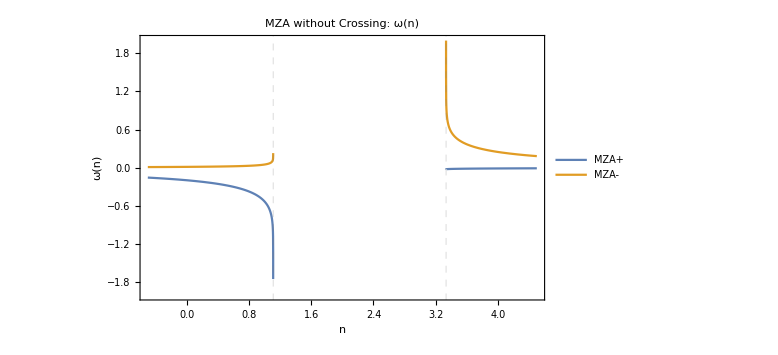

```mathematica
Plot[{ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]},{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{Automatic,{-2,2}},PlotLabel->"MZA without Crossing: ω(n)",FrameLabel->{"n","ω(n)"},Exclusions->{1/0.9,1/0.3},PlotLegends->Placed[{"MZA+","MZA-"},{Right,Top}]]
```

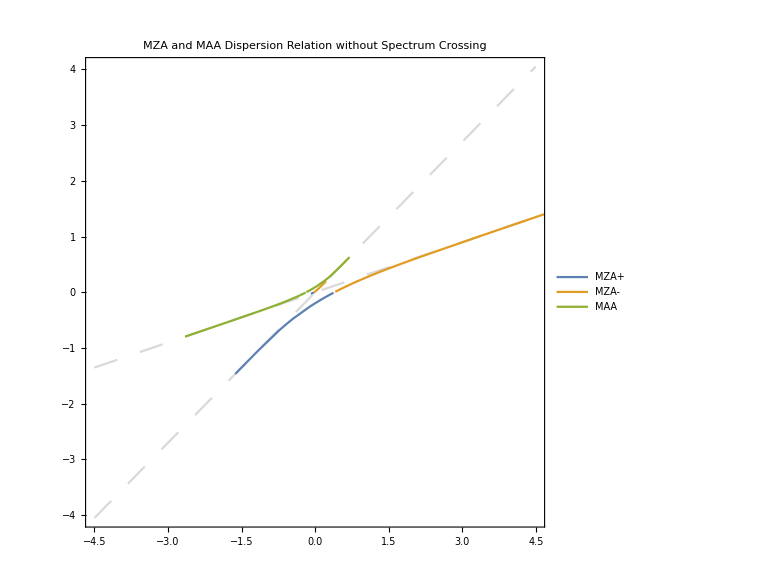

```mathematica
Show[
Plot[{0.3x,0.9x},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,PlotLabel->"MZA and MAA Dispersion Relation without Spectrum Crossing",AspectRatio->1],

ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.3},1}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.3},1}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
```

NonIsotropic Emission

```mathematica
omegaFunMAA1[n_]:=(-IntFun0n[n,0.9,(0.9+0.3)/2]+IntFun0n[n,(0.9+0.3)/2,0.3]-(-IntFun2n[n,0.9,(0.9+0.3)/2]+IntFun2n[n,(0.9+0.3)/2,0.3]))/(4)
```

```mathematica
i0i2[omega_,k_,ct1_,ct2_,g_]:=g ( (1/n-1/n^3)Log[(1-n ct2)/(1-n ct1)] - (ct2-ct1)((ct1+ct2)/2+1/n)/n )
lnArgument[ct1_,ct2_,ct0_]:=Abs[(1-n ct0)^2/((1-n ct1)(1-n ct2))]
```

```mathematica
Limit[ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],n->-Infinity]
```

0.

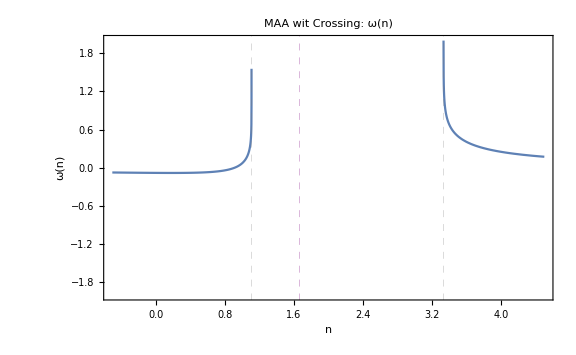

```mathematica
Plot[ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{Automatic,{-2,2}},PlotLabel->"MAA wit Crossing: ω(n)",FrameLabel->{"n","ω(n)"},Exclusions->{1/0.9,1/0.3,1/0.6}]
```

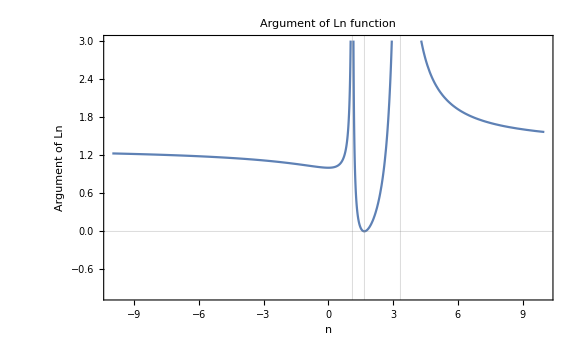

```mathematica
Plot[lnArgument[0.9,0.3,0.6],{n,-10,10},Frame->True,ImageSize->Large,GridLines->{{1/0.3,1/0.6,1/0.9}, {0}},PlotRange->{Automatic,{-1,3}},PlotLabel->"Argument of Ln function",FrameLabel->{"n","Argument of Ln"}]
```

```mathematica
Limit[{n omegaFunMAA1[n],omegaFunMAA1[n]},n->Infinity]
Limit[{n omegaFunMZA[n],omegaFunMZA[n]},n->Infinity]
Limit[{n omegaFunMAA1[n],omegaFunMAA1[n]},n->1/0.3]
```

{-0.0944205,0.}

{Limit[n omegaFunMZA[n],n→∞],Limit[omegaFunMZA[n],n→∞]}

{-∞,-∞}

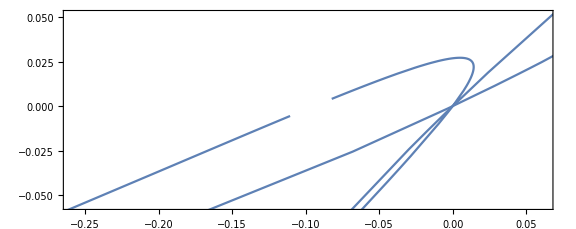

```mathematica
ParametricPlot[
{n omegaFunMAA1[n],omegaFunMAA1[n]},
{n,-20,20},Frame->True,ImageSize->Large]
```

## Direct Approach 1

```mathematica
ContiIntsOriginal[i_,omega_,k_]:=Assuming[omega∈Reals&&k∈Reals,
Integrate[-Sin[theta]((2Pi)/(ArcCos@0.3-ArcCos@0.9)) ( Cos[theta]^i/(1-omega Cos[theta]/k) ),{theta,ArcCos@0.9,ArcCos@0.3}]
];
ContiInts[i_,omega_,k_,theta1_,theta2_]:=(2 k (omega/k)^-i π (Beta[(omega Cos[theta1])/k,1+i,0]-Beta[(omega Cos[theta2])/k,1+i,0]))/(omega (theta1-theta2));
```

```mathematica
ContiInts[0,omega,k,ArcCos@0.9,ArcCos@0.3]
```

-(7.7087 k (-Log[1-(0.9 omega)/k]+Log[1-(0.3 omega)/k]))/omega

```mathematica
ContiAxialSymEqn[omega_,k_,theta1_,theta2_]:=4omega==ContiInts[0,omega,k,theta1,theta2]-ContiInts[2,omega,k,theta1,theta2]
```

```mathematica
ContiAxialSymEqn[omega,0.4,ArcCos@0.9,ArcCos@0.3]//Simplify
```

4 omega==(0.493357 (-Beta[0.75 omega,3,0]+Beta[2.25 omega,3,0]))/omega^3-(3.08348 (-Log[1-2.25 omega]+Log[1-0.75 omega]))/omega

```mathematica
NSolve[ContiAxialSymEqn[omega,0.4,ArcCos@0.9,ArcCos@0.3],omega]
```

NSolve[4 omega==(0.493357 (-Beta[0.75 omega,3,0]+Beta[2.25 omega,3,0]))/omega^3-(3.08348 (-Log[1-2.25 omega]+Log[1-0.75 omega]))/omega,omega]

```mathematica
Table[
omega/.FindRoot[ContiAxialSymEqn[omega,0.4,ArcCos@0.9,ArcCos@0.3],{omega,rootinit}],
{rootinit,-5,5,0.09}]
```

{-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457-1.69337×10^-16 ⅈ,-0.445457+1.61998×10^-16 ⅈ,1.42768-2.98483×10^-17 ⅈ,1.42768-6.88169×10^-17 ⅈ,1.42768+4.5912×10^-16 ⅈ,1.42768-2.4941×10^-17 ⅈ,1.42768+4.66029×10^-17 ⅈ,1.42768+1.37876×10^-15 ⅈ,1.42768-5.07148×10^-17 ⅈ,1.42768+6.70095×10^-17 ⅈ,1.42768-7.76134×10^-17 ⅈ,1.42768-8.93384×10^-17 ⅈ,1.42768-8.20334×10^-17 ⅈ,1.42768-8.36572×10^-17 ⅈ,1.42768-8.03436×10^-17 ⅈ,1.42768-1.03441×10^-16 ⅈ,1.42768-9.54473×10^-17 ⅈ,1.42768-8.34038×10^-17 ⅈ,1.42768-7.46888×10^-17 ⅈ,1.42768-9.97187×10^-17 ⅈ,1.42768-1.02503×10^-16 ⅈ,1.42768-8.28439×10^-17 ⅈ,1.42768-5.24147×10^-17 ⅈ,1.42768-9.50352×10^-17 ⅈ,1.42768-9.01846×10^-17 ⅈ,1.42768-9.58721×10^-17 ⅈ,1.42768-5.22652×10^-17 ⅈ,1.42768-1.11491×10^-16 ⅈ,1.42768-8.82574×10^-17 ⅈ,1.42768-9.07785×10^-17 ⅈ,1.42768-9.62105×10^-17 ⅈ,1.42768-7.26903×10^-17 ⅈ,1.42768-7.84539×10^-17 ⅈ,1.42768-6.9992×10^-17 ⅈ,-0.445457-2.84235×10^-16 ⅈ,1.42768-8.80566×10^-17 ⅈ,-0.445457-2.65928×10^-17 ⅈ,-0.445457-3.13044×10^-17 ⅈ,-0.445457-2.75786×10^-17 ⅈ,-0.445457-2.98863×10^-17 ⅈ,-0.445457-2.65292×10^-17 ⅈ,-0.445457-2.70612×10^-17 ⅈ,-0.445457-2.34447×10^-17 ⅈ,-0.445457-2.5862×10^-17 ⅈ,-0.445457-2.73537×10^-17 ⅈ,-0.445457-2.35693×10^-17 ⅈ,-0.445457-2.65066×10^-17 ⅈ,-0.445457-2.70705×10^-17 ⅈ,-0.445457-2.27763×10^-17 ⅈ,-0.445457-2.06798×10^-17 ⅈ,-0.445457-2.30209×10^-17 ⅈ}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

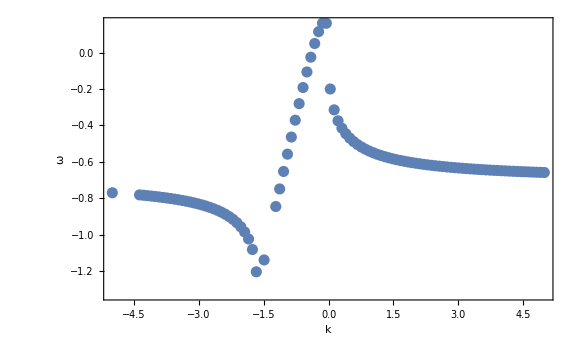

```mathematica
ListPlot[
Table[
{k,omega/.FindRoot[ContiAxialSymEqn[omega,k,ArcCos@0.9,ArcCos@0.3],{omega,-5}]},
{k,-5,5,0.09}],
Frame->True,FrameLabel->{"k","ω"},ImageSize->Large]
```

```mathematica
N@{2441,1293}/1939023
N@{29+7,23+10}/15812
```

{0.00125888,0.000666831}

{0.00227675,0.00208702}

$Aborted

## MZA and Bimodal (non homogeneous)

```mathematica
IntFun0[1,n,0.9,(0.9+0.3)/2]-IntFun0[1,n,(0.9+0.3)/2,0.3];
IntFun2[1,n,0.9,(0.9+0.3)/2]-IntFun2[1,n,(0.9+0.3)/2,0.3]//FullSimplify;
IntFun1[1,n,0.9,(0.9+0.3)/2]-IntFun1[1,n,(0.9+0.3)/2,0.3]//FullSimplify;

i0mza=-IntFun0n[n,0.9,(0.9+0.3)/2]+IntFun0n[n,(0.9+0.3)/2,0.3];
i2mza=-IntFun2n[n,0.9,(0.9+0.3)/2]+IntFun2n[n,(0.9+0.3)/2,0.3]//FullSimplify;
i1mza=-IntFun1n[n,0.9,(0.9+0.3)/2]+IntFun1n[n,(0.9+0.3)/2,0.3]//FullSimplify;

i0mzaabs=g1 IntFun0n[n,c1,c0]+g2 IntFun0n[n,c0,c2];
i2mzaabs=g1 IntFun2n[n,c1,c0]+g2 IntFun2n[n,c0,c2]//FullSimplify;
i1mzaabs=g1 IntFun1n[n,c1,c0]+g2 IntFun1n[n,c0,c2]//FullSimplify;


omegaFunMZA[n_]=(-4(i0mza)(i2mza)+4 i1mza^2+8(i0mza+i2mza))/(-16);


omegaFunMAA1abs[n_]:=(g1 intFun0n[n,c1,c0]+g2 intFun0n[n,c0,c2]-(g1 intFun2n[n,c1,c0]+g2  intFun2n[n,c0,c2]))/(4);
omegaFunMZA1abs[n_]:=(-4(i0mzaabs)(i2mzaabs)+4 i1mzaabs^2+8(i0mzaabs+i2mzaabs))/(-16);
```

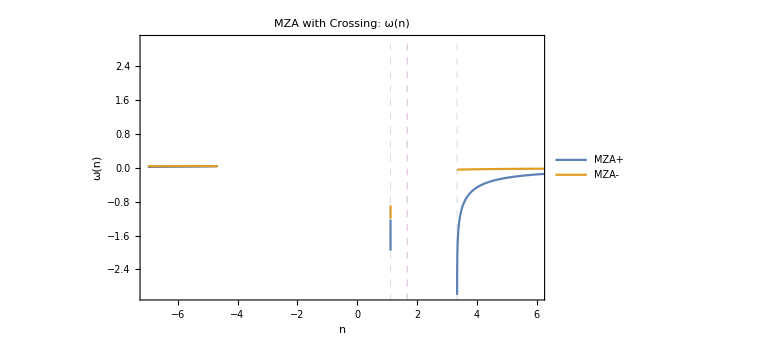

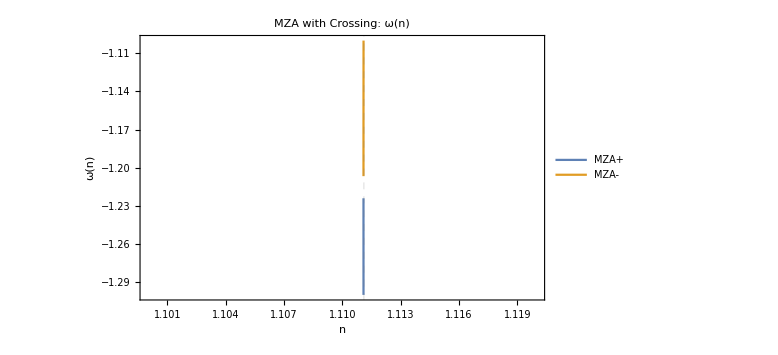

```mathematica
Plot[{ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{-7,6},{-3,3}},PlotLabel->"MZA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},Exclusions->{1/0.9,1/0.3,1/0.6},PlotLegends->Placed[{"MZA+","MZA-"},{Left,Top}]]
Plot[{ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{1.1,1.12},{-1.3,-1.1}},PlotLabel->"MZA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},Exclusions->{1/0.9,1/0.3,1/0.6},PlotLegends->Placed[{"MZA+","MZA-"},{Left,Top}]]
```

```mathematica
Limit[{ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},n->#]&/@{1/0.9,1/0.6,1/0.3,Infinity,-Infinity}
```

{{-∞,-0.639474-36.1614 ⅈ},{-0.126563+3.18086 ⅈ,∞},{-∞,-0.0445055},{0.,0.},{0.,0.}}

Are MZA and MAA some kind of mirror of omega=0?

```mathematica
Table[
{1/0.9-0.000001*n,(1/0.9-0.000001*n)ConAxialSymOmegaNMZA[1/0.9-0.000001*n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMZA[1/0.9-0.000001*n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},
{n,1,30}]
```

{{1.11111,{-2.67285,-0.918925},{-2.40556,-0.827034}},{1.11111,{-2.44834,-0.945857},{-2.20351,-0.851273}},{1.11111,{-2.31286,-0.965766},{-2.08158,-0.869192}},{1.11111,{-2.21407,-0.982547},{-1.99267,-0.884295}},{1.11111,{-2.13543,-0.99757},{-1.92189,-0.897817}},{1.11111,{-2.06951,-1.0115},{-1.86257,-0.910358}},{1.1111,{-2.01233,-1.02474},{-1.81111,-0.922267}},{1.1111,{-1.96147,-1.03752},{-1.76533,-0.933776}},{1.1111,{-1.91535,-1.05005},{-1.72383,-0.945052}},{1.1111,{-1.87289,-1.06246},{-1.68562,-0.956226}},{1.1111,{-1.83328,-1.07489},{-1.64997,-0.967412}},{1.1111,{-1.7959,-1.08745},{-1.61633,-0.978717}},{1.1111,{-1.76026,-1.10026},{-1.58426,-0.990247}},{1.1111,{-1.72594,-1.11345},{-1.55336,-1.00212}},{1.1111,{-1.69254,-1.12717},{-1.52331,-1.01446}},{1.1111,{-1.6597,-1.14159},{-1.49375,-1.02745}},{1.11109,{-1.62702,-1.15698},{-1.46434,-1.0413}},{1.11109,{-1.59403,-1.17367},{-1.43465,-1.05632}},{1.11109,{-1.56008,-1.19219},{-1.40409,-1.07299}},{1.11109,{-1.52417,-1.21346},{-1.37178,-1.09214}},{1.11109,{-1.48435,-1.23936},{-1.33594,-1.11544}},{1.11109,{-1.43516,-1.27527},{-1.29167,-1.14777}},{1.11109,{-1.34887-0.0419465 ⅈ,-1.34887+0.0419465 ⅈ},{-1.21401-0.0377526 ⅈ,-1.21401+0.0377526 ⅈ}},{1.11109,{-1.3428-0.0974085 ⅈ,-1.3428+0.0974085 ⅈ},{-1.20855-0.0876695 ⅈ,-1.20855+0.0876695 ⅈ}},{1.11109,{-1.33698-0.129743 ⅈ,-1.33698+0.129743 ⅈ},{-1.20331-0.116771 ⅈ,-1.20331+0.116771 ⅈ}},{1.11109,{-1.33138-0.154359 ⅈ,-1.33138+0.154359 ⅈ},{-1.19827-0.138927 ⅈ,-1.19827+0.138927 ⅈ}},{1.11108,{-1.32599-0.174637 ⅈ,-1.32599+0.174637 ⅈ},{-1.19342-0.157177 ⅈ,-1.19342+0.157177 ⅈ}},{1.11108,{-1.3208-0.192022 ⅈ,-1.3208+0.192022 ⅈ},{-1.18875-0.172824 ⅈ,-1.18875+0.172824 ⅈ}},{1.11108,{-1.31579-0.207298 ⅈ,-1.31579+0.207298 ⅈ},{-1.18425-0.186573 ⅈ,-1.18425+0.186573 ⅈ}},{1.11108,{-1.31095-0.22095 ⅈ,-1.31095+0.22095 ⅈ},{-1.17989-0.198861 ⅈ,-1.17989+0.198861 ⅈ}}}

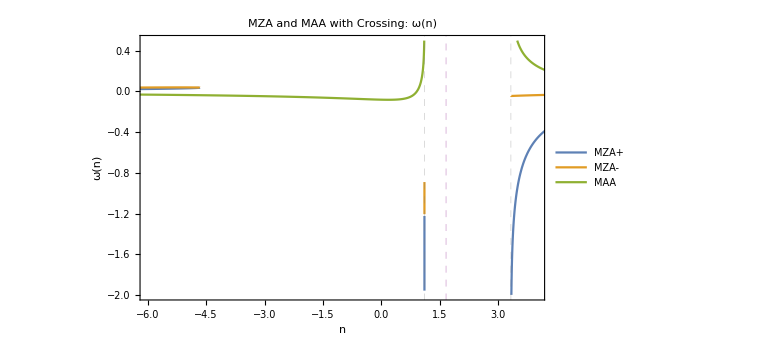

```mathematica
Plot[{ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],
ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{-6,4},{-2,0.5}},PlotLabel->"MZA and MAA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
```

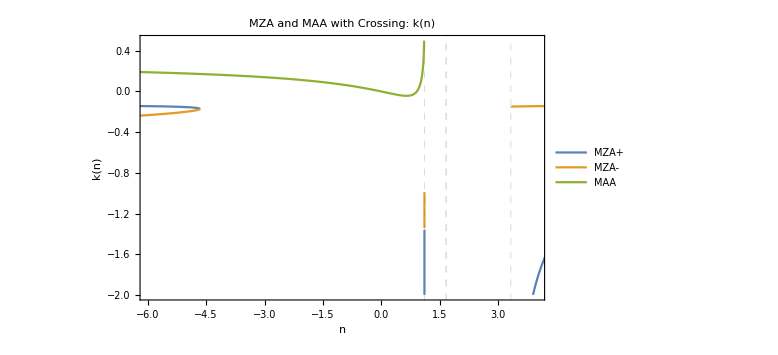

```mathematica
Plot[{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],
n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{-6,4},{-2,0.5}},PlotLabel->"MZA and MAA with Crossing: k(n)",FrameLabel->{"n","k(n)"},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
```

At the limit n->Infinity, we have the omega-k becomes a point:

```mathematica
Limit[{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},n->Infinity]

Limit[{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},n->Infinity]
```

{-0.296523,0.}

{0.283262,0.}

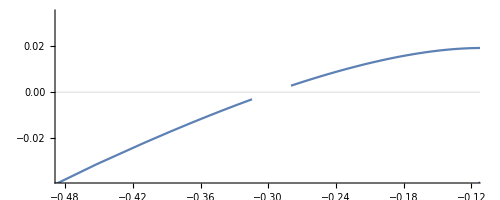

```mathematica
ParametricPlot[{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},
{n,-100,100},GridLines->{{-1,0,1}, {-1,0,1}}]
```

The singularities determines the asymptotic behavior. For n->1/0.3 or n->1/0.9, the omega values can change a lot under a tiny change of n, as also k. So the relative between omega and k becomes linear near these singularities.

Now combine MZA and MAA

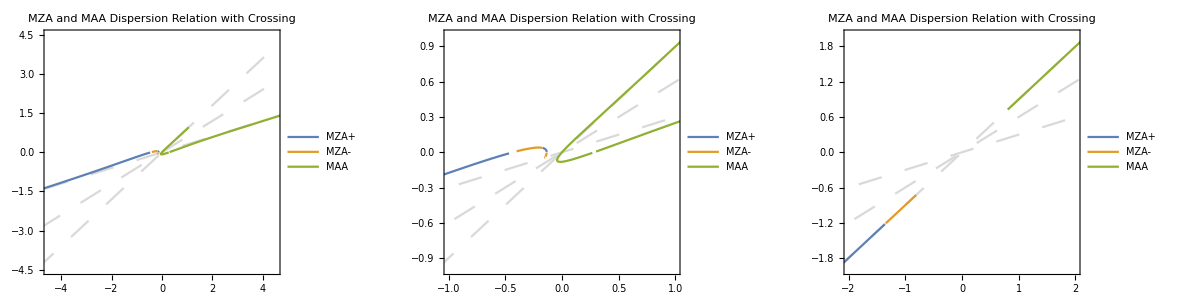

```mathematica
{{Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

],
Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-1,1},{-1,1}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9,1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

],
Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-2,2}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]}
},
{n,1/0.9-0.001,1/0.9+0.001},Frame->True,ImageSize->Large,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9,1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

]}}//Grid
```

```mathematica
Select[Import["export/unstable-regions/lsaGraphc93OmegaRealMZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<0)&]//Length
Select[Import["export/unstable-regions/lsaGraphc93OmegaRealMZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<0)&&(-500<#[[3]]<500)&]//Length

Select[Import["export/unstable-regions/lsaGraphc93OmegaRealMZAm.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&]//Length
Select[Import["export/unstable-regions/lsaGraphc93OmegaRealMZAm.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&&(-100<#[[3]]<100)&]//Length
```

34

34

29

29

```mathematica
Import["export/unstable-regions/lsaGraphc93OmegaRealMZAm.csv"]
```

{{-8.55982,-4.,0},{-8.34584,-3.9,0},{-8.13186,-3.8,0},{-7.91788,-3.7,0},{-7.7039,-3.6,0},{-7.48992,-3.5,0},{-7.27594,-3.4,0},{-7.06196,-3.3,0},{-6.84798,-3.2,0},{-6.634,-3.1,0},{-6.42002,-3.,0},{-6.20604,-2.9,0},{-5.99206,-2.8,0},{-5.77808,-2.7,0},{-5.56408,-2.6,0},{-5.3501,-2.5,0},{-5.13612,-2.4,0},{-4.92214,-2.3,0},{-4.70816,-2.2,0},{-4.49418,-2.1,0},{-4.2802,-2.,0},{-4.06622,-1.9,0},{-3.85224,-1.8,0},{-3.63827,-1.7,0},{-3.42429,-1.6,0},{-3.21031,-1.5,0},{-2.99627,-1.4,0},{-2.7823,-1.3,0},{-2.56832,-1.2,0},{-2.35434,-1.1,0},{-2.14037,-1.,0},{-1.9264,-0.9,0},{-1.71242,-0.8,0},{-1.49846,-0.7,0},{-1.28392,-0.6,0},{-1.06999,-0.5,0},{-0.855957,-0.4,0},{-0.642047,-0.3,0},{-0.428007,-0.2,0},{-0.214064,-0.1,0},{0.619107,0.1,0},{0.866345,0.2,0},{1.13334,0.3,0},{1.41842,0.4,0},{1.71869,0.5,0},{2.03064,0.6,0},{2.35083,0.7,0},{2.67641,0.8,0},{3.00532,0.9,0},{3.3362,1.,0},{3.66819,1.1,0},{4.0008,1.2,0},{4.33375,1.3,0},{4.66688,1.4,0},{5.00011,1.5,0},{5.33339,1.6,0},{5.6667,1.7,0},{6.00002,1.8,0},{6.33334,1.9,0},{6.66667,2.,0},{7.,2.1,0},{7.33333,2.2,0},{7.66667,2.3,0},{8.,2.4,0},{8.33333,2.5,0},{8.66667,2.6,0},{9.,2.7,0},{9.33333,2.8,0},{9.66667,2.9,0},{10.,3.,0},{10.3333,3.1,0},{10.6667,3.2,0},{11.,3.3,0},{11.3333,3.4,0},{11.6667,3.5,0},{12.,3.6,0},{12.3333,3.7,0},{12.6667,3.8,0},{13.,3.9,0},{13.3333,4.,0}}

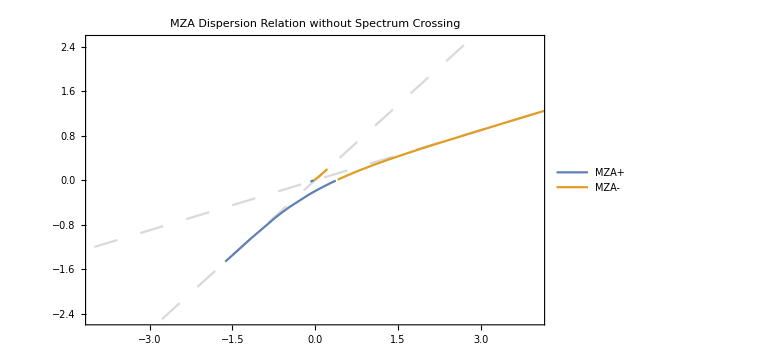
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
lsaGraphc93OmegaRealMZApClean=Select[Import["export/unstable-regions/lsaGraphc93OmegaRealMZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<0)&&(-500<#[[3]]<500)&];
lsaGraphc93OmegaRealMZAmClean=Select[Import["export/unstable-regions/lsaGraphc93OmegaRealMZAm.csv"],(-4<#[[1]]<4)&&(0<#[[2]]<4)&&(-500<#[[3]]<500)&];

Grid[
{{
Show[
Plot[{0.3x,0.9x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,ImagePadding->{{20, 70}, {20, 20}},PlotRange->{{-4,4},{-2.5,2.5}},PlotLabel->"MZA Dispersion Relation without Spectrum Crossing"],

ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
},
{

Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@lsaGraphc93OmegaRealMZApClean,VertexColors->colorf/@Rescale@(#[[3]]&/@lsaGraphc93OmegaRealMZApClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@lsaGraphc93OmegaRealMZApClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA+",
ImageSize->Large,
ImagePadding->{{20, 70}, {20, 20}},
AspectRatio->0.618
],
Plot[{0.9x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-2,2}}],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]
],
Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@lsaGraphc93OmegaRealMZAmClean,VertexColors->colorf/@Rescale@(#[[3]]&/@lsaGraphc93OmegaRealMZAmClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@lsaGraphc93OmegaRealMZAmClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA-",
ImageSize->Large,
ImagePadding->{{20, 70}, {20, 20}},
AspectRatio->0.618
],
Plot[{0.9x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-2,2}}],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]

]
}}
]
```

```mathematica
Export["export/unstable-regions/lsa-DR-93-MZA-Omega-Real.png",%]
```

export/unstable-regions/lsa-DR-93-MZA-Omega-Real.png

```mathematica
lsaGraphc93KRealMZApClean=Select[Import["export/unstable-regions/lsaGraphc93KRealMZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&&(-1<#[[3]]<1)&];
lsaGraphc93KRealMZAmClean=Select[Import["export/unstable-regions/lsaGraphc93KRealMZAm.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&&(-1<#[[3]]<1)&];

Grid[
{{
Show[
Plot[{0.3x,0.9x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,ImagePadding->{{20, 70}, {20, 20}},PlotRange->{{-4,4},{-2.5,2.5}},PlotLabel->"MZA Dispersion Relation without Spectrum Crossing"],

ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
},
{

Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@lsaGraphc93KRealMZApClean,VertexColors->colorf/@Rescale@(#[[3]]&/@lsaGraphc93KRealMZApClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@lsaGraphc93KRealMZApClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k","omega.real"},PlotLabel->"omega.imag for different omega.real vs k: MZA+",
ImageSize->Large,
ImagePadding->{{20, 70}, {20, 20}},
AspectRatio->0.618
],
Plot[{0.9x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-2,2}}],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]

],
Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@lsaGraphc93KRealMZAmClean,VertexColors->colorf/@Rescale@(#[[3]]&/@lsaGraphc93KRealMZAmClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@lsaGraphc93KRealMZAmClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k","omega.real"},PlotLabel->"omega.imag for different omega.real vs k: MZA-",
ImageSize->Large,
ImagePadding->{{20, 70}, {20, 20}},
AspectRatio->0.618
],
Plot[{0.9x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-2,2}}],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9}]

]
}}
]
```

-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Export["export/unstable-regions/lsa-DR-93-MZA-K-Real.png",%]
```

export/unstable-regions/lsa-DR-93-MZA-K-Real.png

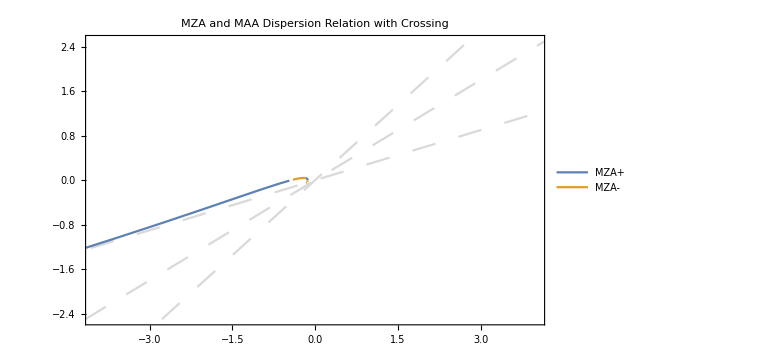
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
lsaGraphc963MZAmClean=Select[Import["export/unstable-regions/lsaGraphc963MZAm.csv"],(-4<#[[1]]<4)&&(0<#[[2]]<4)&&(-1<##[[3]]<1)&];
lsaGraphc963MZApClean=Select[Import["export/unstable-regions/lsaGraphc963MZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<0)&&(-1<##[[3]]<1)&];
Grid[
{{
Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-2.5,2.5}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation with Crossing",Exclusions->{1/0.6,1/0.3}],
ImagePadding->{{40, 60}, {40, 20}}

]
},
{
Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@lsaGraphc963MZApClean,VertexColors->colorf/@Rescale@(#[[3]]&/@lsaGraphc963MZApClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@lsaGraphc963MZApClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA+",
ImageSize->Large,
ImagePadding->{{40, 60}, {40, 20}},
AspectRatio->0.618,PlotRange->{{-4,4},{-2.5,2.5}}
],
Plot[{0.9x,0.6x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-2.5,2.5}}],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation with Crossing",Exclusions->{1/0.6,1/0.3}]

],

Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@lsaGraphc963MZAmClean,VertexColors->colorf/@Rescale@(#[[3]]&/@lsaGraphc963MZAmClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@lsaGraphc963MZAmClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA-",
ImageSize->Large,
ImagePadding->{{40, 60}, {40, 20}},
AspectRatio->0.618,PlotRange->{{-4,4},{-2.5,2.5}}
],
Plot[{0.9x,0.6x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-2.5,2.5}}],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation with Crossing",Exclusions->{1/0.6,1/0.3}]

]
}}
]
```

```mathematica
Export["export/unstable-regions/lsa-DR-963-MZA.png",%]
```

export/unstable-regions/lsa-DR-963-MZA.png

```mathematica
lsaGraphc963KRealMZApClean=Select[Import["export/unstable-regions/lsaGraphc963-omegakKRealMZApPoints.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<0)&&(-1<##[[3]]<1)&];

Grid[
{{
Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-2.5,2.5}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation with Crossing",Exclusions->{1/0.6,1/0.3}],
ImagePadding->{{40, 60}, {40, 20}}

]

,

Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@lsaGraphc963KRealMZApClean,VertexColors->colorf/@Rescale@(#[[3]]&/@lsaGraphc963KRealMZApClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@lsaGraphc963KRealMZApClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA+",
ImageSize->Large,
ImagePadding->{{40, 60}, {40, 20}},
AspectRatio->0.618,PlotRange->{{-4,4},{-2.5,2.5}}
],
Plot[{0.9x,0.6x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-2.5,2.5}}],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4,4},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA Dispersion Relation with Crossing",Exclusions->{1/0.6,1/0.3}]

]

}}
]
```

-Graphics-

So the line is there but missed by the default plot sampling.

```mathematica
parametricPltData963=Table[{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]}
},
{n,-10,10,10^(-5)}]//Quiet;
```

$Aborted

```mathematica
Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
,Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

]
```

```mathematica
(*Export["DR-omega-k-direct-continuous-two-regions-dr-crossing.png",%]*)
```

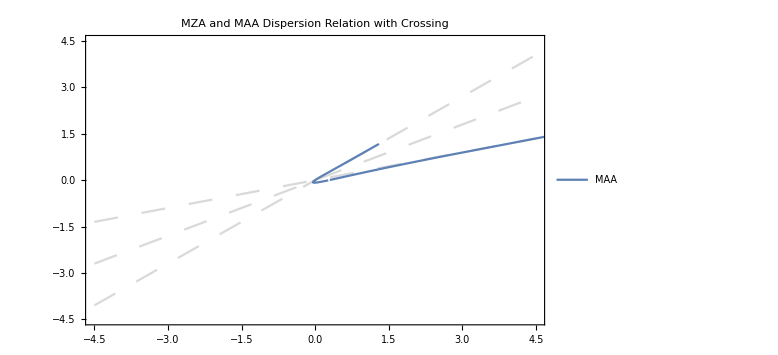

```mathematica
Show[Plot[{0.9x,0.6x,0.3x},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]}
,
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLegends->Placed[{"MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9,1/0.6,1/0.3}]

]
```

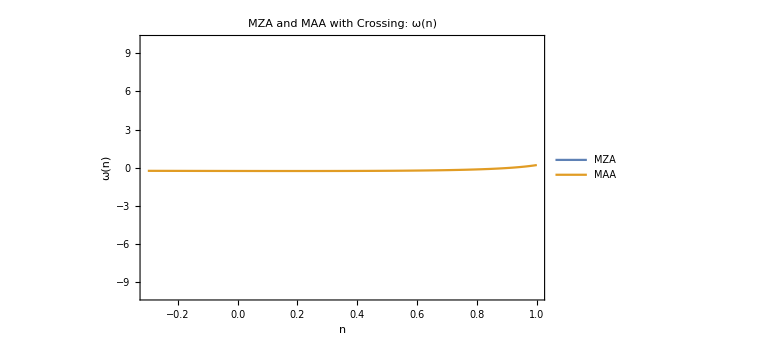

```mathematica
Plot[{ConAxialSymOmegaNMZA[n,{{{0.9,0.6},-Pi},{{0.6,0.3},Pi}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3Pi},{{0.6,0.3},-3Pi}}]},{n,-0.3,1},Frame->True,ImageSize->Large,PlotRange->{Automatic,{-10,10}},GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotLabel->"MZA and MAA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},PlotLegends->Placed[{"MZA","MAA"},{Left,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
```

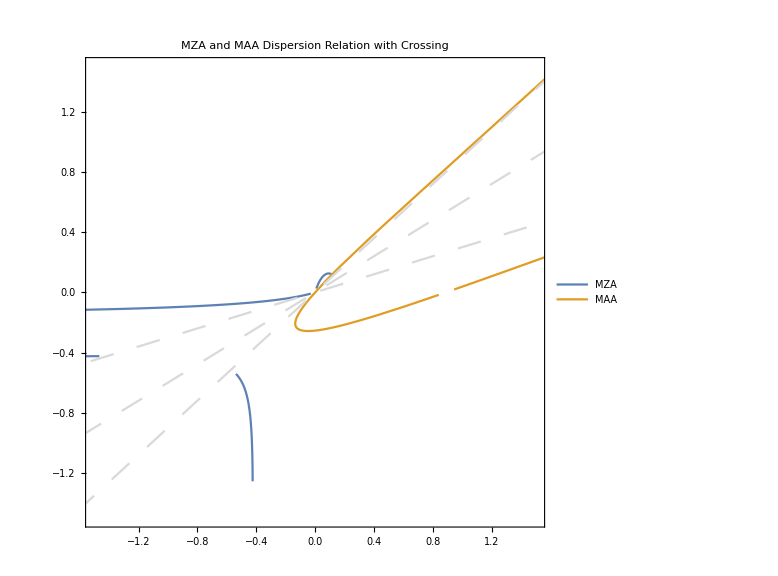

```mathematica
Show[
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3Pi},{{0.6,0.3},-3Pi}}],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3Pi},{{0.6,0.3},-3Pi}}]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3Pi},{{0.6,0.3},-3Pi}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3Pi},{{0.6,0.3},-3Pi}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLegends->Placed[{"MZA","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9}],
Plot[{0.9x,0.6x,0.3x},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]]]
]
```

```mathematica
Limit[{n ,1}omegaFunMAA1abs[n],n->Infinity]//FullSimplify
Limit[{n ,1}omegaFunMZA1abs[n],n->Infinity]//FullSimplify
```

{Limit[1/4 n (g2 intFun0n[n,c0,c2]+g1 intFun0n[n,c1,c0]-g2 intFun2n[n,c0,c2]-g1 intFun2n[n,c1,c0]),n→∞],Limit[1/4 (g2 intFun0n[n,c0,c2]+g1 intFun0n[n,c1,c0]-g2 intFun2n[n,c0,c2]-g1 intFun2n[n,c1,c0]),n→∞]}

{1/4 (c1^2 g1-c2^2 g2+c0^2 (-g1+g2)+2 (-g1+g2) Log[Abs[c0]]+2 g1 Log[Abs[c1]]-2 g2 Log[Abs[c2]]),0}

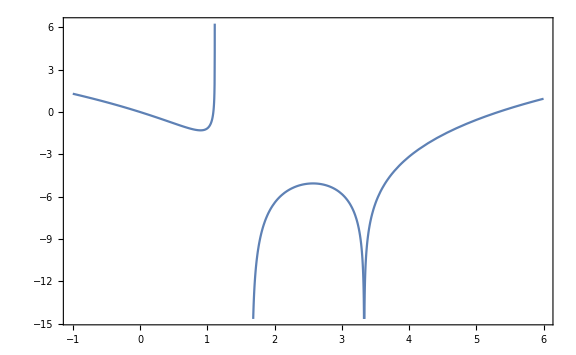

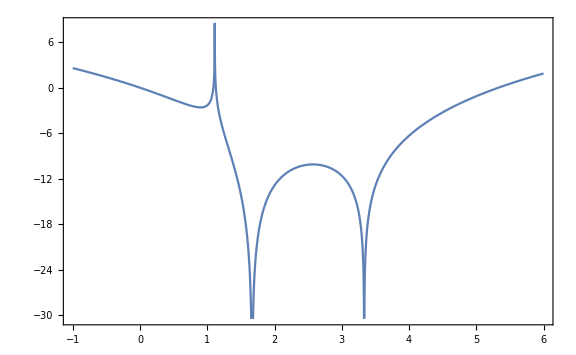

```mathematica
Plot[
Log[(1-n 0.6)^(g1-g2)/( (1-n 0.9)^g1 (1-n 0.3)^g2 )]/.{g1->1,g2->-2},
{n,-1,6},Frame->True,ImageSize->Large]
Plot[
Log[(1-n 0.6)^(g1-g2)/( (1-n 0.9)^g1 (1-n 0.3)^g2 )]/.{g1->2,g2->-4},
{n,-1,6},Frame->True,ImageSize->Large]
```

```mathematica
omegaFunMZAGeneral[1,0.9,0.3,0.6,1,1]
```

1/16 (-(4 ((c0 g1-c1 g1-c0 g2+c2 g2) n+g1 Log[(-1+c0 n)/(-1+c1 n)]+g2 Log[(-1+c2 n)/(-1+c0 n)])^2)/n^4+1/n^3 2 ((g1 (Log[1-c0 n]-Log[1-c1 n]))/n+(g2 (-Log[1-c0 n]+Log[1-c2 n]))/n) (n (-2 c1 g1+2 c0 (g1-g2)-c1^2 g1 n+c0^2 (g1-g2) n+c2 g2 (2+c2 n))+2 g1 Log[(-1+c0 n)/(-1+c1 n)]+2 g2 Log[(-1+c2 n)/(-1+c0 n)])-8 ((g1 (Log[1-c0 n]-Log[1-c1 n]))/n+(g2 (-Log[1-c0 n]+Log[1-c2 n]))/n+1/(2 n^3)(n (-2 c1 g1+2 c0 (g1-g2)-c1^2 g1 n+c0^2 (g1-g2) n+c2 g2 (2+c2 n))+2 g1 Log[(-1+c0 n)/(-1+c1 n)]+2 g2 Log[(-1+c2 n)/(-1+c0 n)])))

```mathematica
omegaFunMZAGeneral[n_,c1_,c2_,c0_,g1_,g2_]=(-4(i0mzaabs)(i2mzaabs)+4 i1mzaabs^2+8(i0mzaabs+i2mzaabs))/(-16);
```

```mathematica
Table[
Limit[
n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}],
n->Infinity],
{g1,-3,3,1},{g2,-3,3,1}]-
Table[
Limit[
n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}],
n->-Infinity],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.

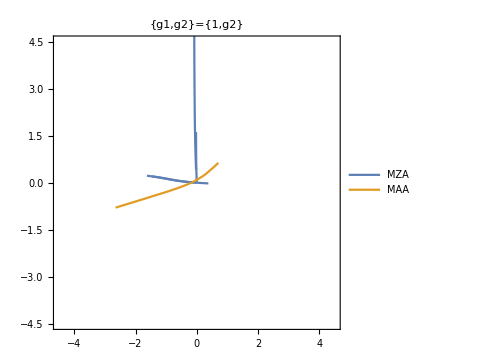

```mathematica
drtableH1=Table[
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},g1}}],ConAxialSymOmegaNMZA[n,{{{0.9,0.3},g1}}]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.3},g1}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.3},g1}}]}
},
{n,-50,50},Frame->True,ImageSize->Medium,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA","MAA"},{Left,Top}],PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}",Exclusions->{1/0.9,1/0.6,1/0.3}],
{g1,{1}}]
```

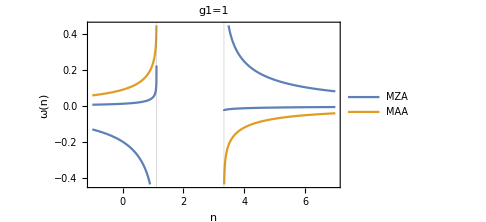

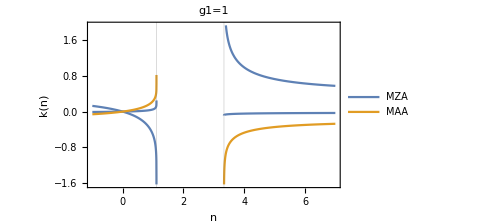

```mathematica
Plot[
{ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.3},1}}]},
{n,-1,7},Frame->True,FrameLabel->{"n","ω(n)"},ImageSize->Medium,GridLines->{{1/0.3,1/0.9}, None},PlotLegends->Placed[{"MZA","MAA"},{Right,Top}],PlotLabel->"g1=1",Exclusions->{1/0.9,1/0.3}]

Plot[
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.3},1}}],n ConAxialSymOmegaNMAA[n,{{{0.9,0.3},1}}]},
{n,-1,7},Frame->True,FrameLabel->{"n","k(n)"},ImageSize->Medium,GridLines->{{1/0.3,1/0.9}, None},PlotLegends->Placed[{"MZA","MAA"},{Right,Top}],PlotLabel->"g1=1",Exclusions->{1/0.9,1/0.3}]
```

```mathematica
drtable1=Table[
Show[
Plot[{0.9x,0.6x,0.3x},{x,-6,6},PlotStyle->Directive[LightGray,Dashing[0.03]]],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[2]]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}]}
},
{n,-50,50},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],Exclusions->{1/0.9,1/0.6,1/0.3}],Frame->True,ImageSize->Medium,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}"
],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
drtable2=Table[
Show[
Plot[{0.9x,0.4x,0.3x},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]]],
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[1]]},
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[2]],ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[2]]},
{n ConAxialSymOmegaNMAA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}],ConAxialSymOmegaNMAA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}]}
},
{n,-50,50},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],Exclusions->{1/0.9,1/0.4,1/0.3}],Frame->True,ImageSize->Medium,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}"
],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
Export["DR-omega-k-continuous-table-0.9-0.6-0.3.png",drtable1]
```

DR-omega-k-continuous-table-0.9-0.6-0.3.png

```mathematica
Export["DR-omega-k-continuous-table-0.9-0.4-0.3.png",drtable2]
```

DR-omega-k-continuous-table-0.9-0.4-0.3.png

```mathematica
diffg1g2knPlt=Table[
Plot[
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[1]],n ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[2]],n ConAxialSymOmegaNMAA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}]},
{n,-1,7},Frame->True,FrameLabel->{"n","k(n)"},ImageSize->Medium,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}",Exclusions->{1/0.9,1/0.6,1/0.3}],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
diffg1g2knPlt2=Table[
Plot[
{n ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[1]],n ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[2]],n ConAxialSymOmegaNMAA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}]},
{n,-1,7},Frame->True,FrameLabel->{"n","k(n)"},ImageSize->Medium,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.4,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}",Exclusions->{1/0.9,1/0.4,1/0.3}],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
Export["DR-k-of-n-for-different-spectra-table-0.9-0.6-0.3.png",diffg1g2knPlt]
```

DR-k-of-n-for-different-spectra.png

```mathematica
Export["DR-k-of-n-for-different-spectra-table-0.9-0.4-0.3.png",diffg1g2knPlt2]
```

DR-k-of-n-for-different-spectra-table-0.9-0.4-0.3.png

```mathematica
diffg1g2omeganPlt=Table[
Plot[
{ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}][[2]],ConAxialSymOmegaNMAA[n,{{{0.9,0.6},g1},{{0.6,0.3},g2}}]},
{n,-7,7},Frame->True,FrameLabel->{"n","ω(n)"},ImageSize->Medium,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}",Exclusions->{1/0.9,1/0.6,1/0.3}],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
diffg1g2omeganPlt2=Table[
Plot[
{ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[1]],ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}][[2]],ConAxialSymOmegaNMAA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}]},
{n,-1,7},Frame->True,FrameLabel->{"n","ω(n)"},ImageSize->Medium,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.4,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}",Exclusions->{1/0.9,1/0.4,1/0.3}],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
Export["DR-omega-of-n-for-different-spectra-table-0.9-0.6-0.3.png",diffg1g2omeganPlt]
```

DR-omega-of-n-for-different-spectra.png

```mathematica
Export["DR-omega-of-n-for-different-spectra-table-0.9-0.4-0.3.png",diffg1g2omeganPlt2]
```

DR-omega-of-n-for-different-spectra-table-0.9-0.4-0.3.png

```mathematica
diffg1g2Plt=Table[
Plot[
ConAxialSymOmegaNMZA[n,{{{0.9,0.4},g1},{{0.4,0.3},g2}}],
{n,-1,7},Frame->True,ImageSize->Small,GridLines->{{1/0.3,1/0.6,1/0.9}, None},PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}",Exclusions->{1/0.9,1/0.6,1/0.3}],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
Export["export/diffg1g2Plt.png",diffg1g2Plt]
```

export/diffg1g2Plt.png

```mathematica
Assuming[a∈Reals&&b∈Reals,
Integrate[1/x,{x,a,b}]
]
```

ConditionalExpression[Log[b/a],0<a<b]

```mathematica
Eigensystem[
{
{i0/2,0,0,-i1/2},
{0,-(i0-i2)/4,0,0},
{0,0,-(i0-i2)/4,0},
{i1/2,0,0,-i2/2}
}
]//Grid
```

1/4 (-i0+i2) | 1/4 (-i0+i2) | 1/4 (i0-i2-√(i0^2-4 i1^2+2 i0 i2+i2^2)) | 1/4 (i0-i2+√(i0^2-4 i1^2+2 i0 i2+i2^2))
{0,0,1,0} | {0,1,0,0} | {-(-i0-i2+√(i0^2-4 i1^2+2 i0 i2+i2^2))/(2 i1),0,0,1} | {-(-i0-i2-√(i0^2-4 i1^2+2 i0 i2+i2^2))/(2 i1),0,0,1}

## Limits

```mathematica
DConAxialSymOmegaNMZA[n_]=D[ConAxialSymOmegaNMZA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],n];
DConAxialSymOmegaNMAA[n_]=D[ConAxialSymOmegaNMAA[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],n];
```

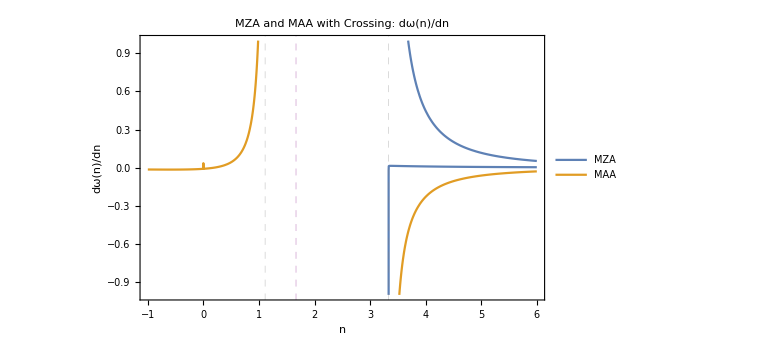

```mathematica
Plot[{DConAxialSymOmegaNMZA[n],DConAxialSymOmegaNMAA[n]},{n,-1,6},Frame->True,ImageSize->Large,PlotRange->{Automatic,{-1,1}},GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotLabel->"MZA and MAA with Crossing: dω(n)/dn",FrameLabel->{"n","dω(n)/dn"},PlotLegends->Placed[{"MZA","MAA"},{Right,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
```

```mathematica
Limit[ConAxialSymOmegaNMZA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{Infinity,-Infinity}
Limit[n ConAxialSymOmegaNMZA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{Infinity,-Infinity}
```

{{0,0},{0,0}}

{{1/8 (c0^2 g1-c1^2 g1-c0^2 g2+c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2]-√((-4 c0 g1+c0^2 g1+4 c1 g1-c1^2 g1+4 c0 g2-c0^2 g2-4 c2 g2+c2^2 g2-2 g1 Log[c1/c0]-2 g2 Log[c0/c2]) (4 c0 g1+c0^2 g1-4 c1 g1-c1^2 g1-4 c0 g2-c0^2 g2+4 c2 g2+c2^2 g2-2 g1 Log[c1/c0]-2 g2 Log[c0/c2]))),1/8 (c0^2 g1-c1^2 g1-c0^2 g2+c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2]+√((-4 c0 g1+c0^2 g1+4 c1 g1-c1^2 g1+4 c0 g2-c0^2 g2-4 c2 g2+c2^2 g2-2 g1 Log[c1/c0]-2 g2 Log[c0/c2]) (4 c0 g1+c0^2 g1-4 c1 g1-c1^2 g1-4 c0 g2-c0^2 g2+4 c2 g2+c2^2 g2-2 g1 Log[c1/c0]-2 g2 Log[c0/c2])))},{1/8 (c0^2 g1-c1^2 g1-c0^2 g2+c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2]+√((-4 c0 g1-c0^2 g1+4 c1 g1+c1^2 g1+4 c0 g2+c0^2 g2-4 c2 g2-c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2]) (4 c0 g1-c0^2 g1-4 c1 g1+c1^2 g1-4 c0 g2+c0^2 g2+4 c2 g2-c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2]))),1/8 (c0^2 g1-c1^2 g1-c0^2 g2+c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2]-√((-4 c0 g1-c0^2 g1+4 c1 g1+c1^2 g1+4 c0 g2+c0^2 g2-4 c2 g2-c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2]) (4 c0 g1-c0^2 g1-4 c1 g1+c1^2 g1-4 c0 g2+c0^2 g2+4 c2 g2-c2^2 g2+2 g1 Log[c1/c0]+2 g2 Log[c0/c2])))}}

```mathematica
Limit[ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{Infinity,-Infinity}
Limit[n ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{Infinity,-Infinity}
```

{0,0}

{1/8 (-c0^2 g1+c1^2 g1+c0^2 g2-c2^2 g2-2 g1 Log[c1/c0]-2 g2 Log[c0/c2]),1/8 (-c0^2 g1+c1^2 g1+c0^2 g2-c2^2 g2-2 g1 Log[c1/c0]-2 g2 Log[c0/c2])}

```mathematica
Limit[ConAxialSymOmegaNMZA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c1}
```

{{Limit[1/4 ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c1],Limit[1/4 ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c1]}}

```mathematica
Limit[ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c1}
```

{c1 DirectedInfinity[-Sign[(-1+c1^2) g1]]}

```mathematica
Limit[n ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c1}
```

{DirectedInfinity[g1-c1^2 g1]}

```mathematica
Limit[ConAxialSymOmegaNMZA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c2}
```

{{Limit[1/4 ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c2],Limit[1/4 ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c2]}}

```mathematica
Limit[n ConAxialSymOmegaNMZA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c2}
```

{{Limit[1/4 n ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c2],Limit[1/4 n ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c2]}}

```mathematica
Limit[ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c2}
```

{c2 DirectedInfinity[-g2+c2^2 g2]}

```mathematica
Limit[n ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c2}
```

{DirectedInfinity[(-1+c2^2) g2]}

```mathematica
Limit[ConAxialSymOmegaNMZA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c0}
```

{{Limit[1/4 ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c0],Limit[1/4 ((g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)+(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+√((-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)-2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)) (-(g1 Log[(1-c1 n)/(1-c0 n)])/n+(g1 (-(-c0+c1) (c0+c1+2/n)+(2 Log[(-1+c0 n)/(-1+c1 n)])/n^2))/(2 n)-(g2 Log[(1-c0 n)/(1-c2 n)])/n+(g2 (-(c0-c2) (c0+c2+2/n)+(2 Log[(-1+c2 n)/(-1+c0 n)])/n^2))/(2 n)+2 ((g1 (c0-c1+Log[(-1+c0 n)/(-1+c1 n)]/n))/n+(g2 (-c0+c2+Log[(-1+c2 n)/(-1+c0 n)]/n))/n)))),n→1/c0]}}

```mathematica
Limit[ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c0}
```

{c0 DirectedInfinity[(-1+c0^2) (g1-g2)]}

```mathematica
Limit[n ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,c2},g2}}],n->#]&/@{1/c0}
```

{DirectedInfinity[(-1+c0^2) (g1-g2)]}

```mathematica
Limit[ConAxialSymOmegaNMAA[n,{{{c1,c0},g1},{{c0,1},g2}}],n->#]&/@{1/1}
```

{1/8 (-2 c0 g1-c0^2 g1+2 c1 g1+c1^2 g1-3 g2+2 c0 g2+c0^2 g2-2 g2 Log[1/(-1+c0)]-2 g2 Log[-1+c0]-2 g1 Log[(-1+c0)/(-1+c1)]-2 g1 Log[(-1+c1)/(-1+c0)])}